# Section 3.2 Plots

Trevor Swan’s Plots for HW6 in MATH224:
This was exclusively written by me, as I never copied any code from ChatGPT or the internet

## Question 3.2.3

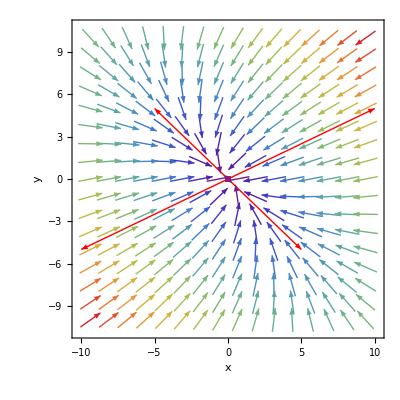

```mathematica
(* Set up plot components for part c*)
parentPlot =VectorPlot[{-5*x+-2*y,-1*x+-4*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorScale->{Small,0.5,None},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{-5,-2},{-1,-4}}];
eigenLines1=Graphics[{Red,Arrow[{{0,0},#}]&/@(5*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrow[{{0,0},#}]&/@(-5*eigenVectors)}];
(* Display the plot for c *)
Show[parentPlot, eigenLines1, eigenLines2, PlotRange-> All]
```

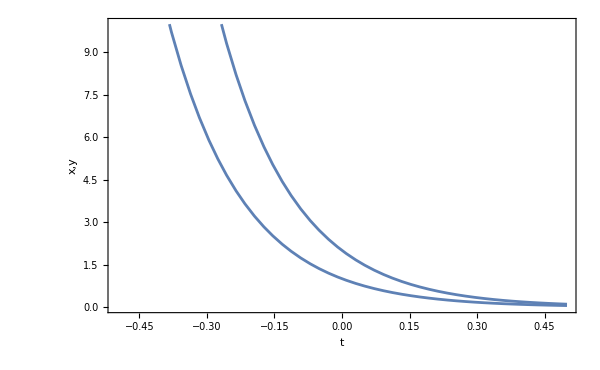

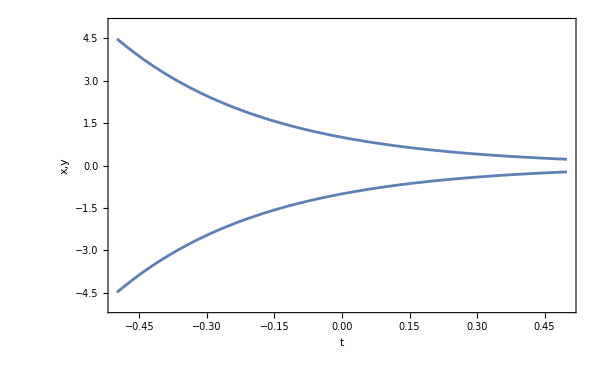

```mathematica
(* Set up plot contents for d.1 *)
componentd1x = Plot[2*Exp[-6*t],{t, -0.5,0.5}, PlotRange->{Automatic,{0,10}},Frame->True,FrameLabel->{"t","x,y"}];
componentd1y = Plot[Exp[-6*t],{t, -0.5,0.5}, PlotRange->{Automatic,{0,10}}];
(*Set up plot contents for d.2*)
componentd2x = Plot[Exp[-3*t],{t, -0.5, 0.5}, PlotRange->{Automatic,{-5,5}},Frame->True,FrameLabel->{"t","x,y"}];
componentd2y = Plot[-1*Exp[-3*t],{t, -0.5, 0.5}, PlotRange->{Automatic,{-5,5}}];
(* Display the two needed plots for d *)
Show[componentd1x, componentd1y]
Show[componentd2x, componentd2y]
```

## Question 3.2.5

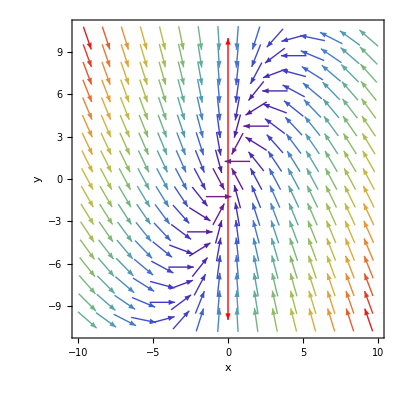

```mathematica
(* Set up plot components for part c*)
parentPlot =VectorPlot[{-(1/2)*x+0*y,1*x+-(1/2)*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorScale->{Small,0.5,None},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{-1/2,0},{1,-1/2}}];
eigenLines1=Graphics[{Red,Arrow[{{0,0},#}]&/@(10*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrow[{{0,0},#}]&/@(-10*eigenVectors)}];
(* Display the plot for c *)
Show[parentPlot, eigenLines1, eigenLines2, PlotRange-> All]
```

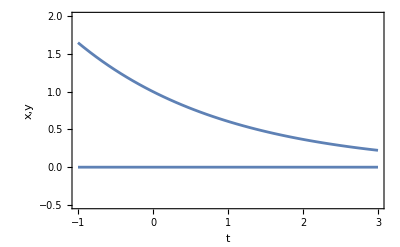

```mathematica
(* Set up plot contents for d *)
componentd1x = Plot[0*Exp[-(1/2)*t],{t, -1,3}, PlotRange->{Automatic,{-0.5,2}},Frame->True,FrameLabel->{"t","x,y"}];
componentd1y = Plot[Exp[-(1/2)*t],{t, -1,3}, PlotRange->{Automatic,{-0.5,2}}];
(* Display the one needed plot for d *)
Show[componentd1x, componentd1y]
```